(0.
0.6
1.2
1.8
2.4
3.
3.6
4.2
4.8
5.4
6.) (0.0965324
0.11557
0.132937
0.146919
0.156003
0.159155
0.156003
0.146919
0.132937
0.11557
0.0965324)

0.13228

0.13228+4.71518×10^-18 x

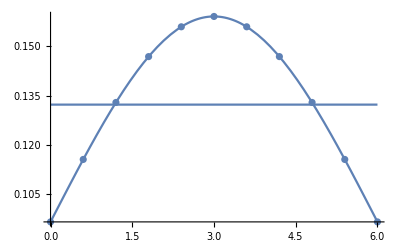

```mathematica
a=0;b=6;n=10;
h=(b-a)/n;
XDT={}; YDT={};
For[i=0,i≤n,i++, xdata[i]=N[a+i*h];ydata[i]=N[1/(2π)*Exp[-1/18(xdata[i])^2+1/3(xdata[i])-1/2]]; XDT=Append[XDT, xdata[i]];YDT=Append[YDT, ydata[i]];];
MatrixForm[XDT]MatrixForm[YDT]

Array[xdata,{n+1,0}];Array[ydata,{n+1,0}];
Clear[x]
ex=∑_(i=0)^n xdata[i];ey=∑_(i=0)^n ydata[i];exx=∑_(i=0)^n xdata[i]^2;
exy=∑_(i=0)^n xdata[i]*ydata[i]; 
eyy=∑_(i=0)^n ydata[i]^2;
 a=(ey*exx-ex*exy)/((n+1)*exx-ex^2); b=((n+1)*exy-ex*ey)/((n+1)*exx-ex^2);
g[x_]:=a+b*x;
g[x]
data=Table[{N[xdata[i]], N[ydata[i]]},{i,0,n}];
Clear[a,b]; rules= FindFit[data,a+b*x, {a,b},x];y=a+b*x/.rules
gr1:=Plot[N[1/(2π)*Exp[-1/18 x^2+1/3 x-1/2]],{x,0,6}];
gr2:= ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
gr3:=Plot[y,{x,0,6}];
Show[{gr1,gr2,gr3}]
```